```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
CaculateComplexVectMatrix[v_]:={ReIm[v[[1]]],ReIm[v[[2]]]};

ComplexEigenTest[eig_,eigV_,n_]:=Module[
{λ,v,x,y,B,C},
(*取出第n个特征值λ，特征向量v*)
λ=eig[[n]];v=eigV[[All,n]];
B = ({{Re(λ), Im(λ)}, {-Im(λ), Re(λ)}});
C=CaculateComplexVectMatrix[v];
C.B.Inverse[C]
];


PlotMatrix[M_]:=Module[
{a,b,c,d,MM,MM1,MM2,MM3,MM4,eigen,Eigen,isEigenComplex,C1,C2,u,σ,v,start,end,len},

{{a,b},{c,d}}=M;
MM = {{a, b}, {c, d}};

{eigen,Eigen}=N[Eigensystem[MM]];
Eigen=N[Transpose[Normalize/@Eigen]];
isEigenComplex=Not[Element[eigen[[1]],Reals]];
MM1=N[Eigen . DiagonalMatrix[eigen] . Inverse[Eigen]];
MM2=If[isEigenComplex,N[ComplexEigenTest[eigen,Eigen,1]],MM];
MM3=If[isEigenComplex,N[ComplexEigenTest[eigen,Eigen,2]],MM];
C1=CaculateComplexVectMatrix[Eigen[[All,1]]];
C2=CaculateComplexVectMatrix[Eigen[[All,2]]];

{u,σ,v}=N[SingularValueDecomposition[MM]];
MM4=N[u.σ.ConjugateTranspose[v]];

start=-30;end=-start;len=end;

MatrixForm[
{
{Show[
{

StreamPlot[MM.{x,y},{x,start,end},{y,start,end},StreamStyle->{Opacity[0.3]}],
VectorPlot[MM.{x,y},{x,start,end},{y,start,end},VectorStyle->Opacity[0.1]],
(*映射后vAvd等高*)
ContourPlot[{x,y}.MM.{x,y},{x,start,end},{y,start,end},ContourShading->None],
(*映射后的向量长度*)
(*ContourPlot[1/Norm[Inverse[MM].{x,y}],{x,start,end},{y,start,end},ContourShading->None],*)

(*原坐标系*)
ListPlot[{0},PlotStyle->{Gray,PointSize[Medium]}],
Graphics[{Gray,Opacity[0.9],Thick,Arrow[{{0,0},{1,0}*4}]}],
Graphics[{Gray,Opacity[0.8],Thick,Arrow[{{0,0},{0,1}*4}]}],
ParametricPlot[3*{ Cos[t], Sin[t]},{t,0,2Pi},ColorFunction->Function[{x,y,t},ColorData["Rainbow"][t]]],
(*蓝色变换后矩阵向量*)
Graphics[{Red,Opacity[0.7],Thick,Arrow[{{0,0},MM[[All,1]]*6}]}],
Graphics[{Blue,Opacity[0.7],Thick,Arrow[{{0,0},MM[[All,2]]*6}]}],
ListPlot[{MM[[All,1]]*3.,MM[[All,2]]*3.},PlotStyle->{Blue,PointSize[Large]}],
(*单位圆被映射成椭圆*)
ParametricPlot[MM.{Cos[t], Sin[t]}*3,{t,0,2Pi},ColorFunction->Function[{x,y,t},ColorData["Rainbow"][t]]],
Array[i|->Graphics[{ColorData["Rainbow"][i/50],Opacity[0.9],Thin,Arrowheads[0.01],Arrow[{{0,0},2.8*MM.{Cos[i/50*2Pi],Sin[i/50*2Pi]}}]}],50]
}
~Join~
If[isEigenComplex,
{
Graphics[{Cyan,Opacity[0.8],Thick,Arrow[{{0,0},C1[[All,1]]*3}]}],
Graphics[{Cyan,Opacity[0.8],Thick,Arrow[{{0,0},C1[[All,2]]*3}]}],
Graphics[{Darker[Cyan],Opacity[0.8],Thick,Arrow[{{0,0},MM.C1[[All,1]]*6}]}],
Graphics[{Darker[Cyan],Opacity[0.8],Thick,Arrow[{{0,0},MM.C1[[All,2]]*6}]}],

Graphics[{Yellow,Opacity[0.8],Thick,Arrow[{{0,0},C2[[All,1]]*4}]}],
Graphics[{Yellow,Opacity[0.8],Thick,Arrow[{{0,0},C2[[All,2]]*4}]}],
Graphics[{Darker[Yellow],Opacity[0.8],Thick,Arrow[{{0,0},MM.C2[[All,1]]*8}]}],
Graphics[{Darker[Yellow],Opacity[0.8],Thick,Arrow[{{0,0},MM.C2[[All,2]]*8 }]}]
}
,
{
(*绿色实数特征值*)
Graphics[{Green,Opacity[0.8],Thick,Arrow[{{0,0},Eigen[[All,1]]*eigen[[1]]*5}]}],
Graphics[{Green,Opacity[0.8],Thick,Arrow[{{0,0},Eigen[[All,2]]*eigen[[2]]*5}]}],
		ListPlot[{Eigen[[All,1]]*2.5,Eigen[[All,2]]*2.5},PlotStyle->{Green,PointSize[Large]}]
}]
~Join~
{
(*粉色奇艺值 u 或者 M.v *)
Graphics[{Pink,Opacity[0.9],Thick,Arrow[{{0,0},u[[All,1]]*σ[[1,1]]*3}]}],
Graphics[{Pink,Opacity[0.8],Thick,Arrow[{{0,0},u[[All,2]]*σ[[2,2]]*3}]}],
		  ListPlot[{MM.v[[All,1]]*3.,MM.v[[All,2]]*3.},PlotStyle->{Pink,PointSize[Large]}]
},
ImageSize->{600,600}
]
},
{MatrixForm[N[MM]],N[MM1]==N[MM],N[MM2]==N[MM],N[MM3]==N[MM],N[MM4]==N[MM]},
MatrixForm/@{MM1,MM2,MM3,MM4},
MatrixForm/@{C1,C2},
MatrixForm/@{eigen,N[Eigen]},
MatrixForm/@{u,σ,v}

(*{StreamPlot[MM.(MM.{x,y}),{x,start,end},{y,start,end}]},
{StreamPlot[MM.(MM.(MM.{x,y})),{x,start,end},{y,start,end}]}*)
(*ParametricPlot3D[{Dot[MM,{x,y}][[1]],Dot[MM,{x,y}][[2]],Norm[Dot[MM,{x,y}]]},{x,start/3,end/3},{y,start/3,end/3},
PlotRange->{{-len,len},{-len,len},{-len,len}},Axes->True,AxesStyle->{Red,Green,Blue},ImageSize->{500,500}]*)

}
]

];

DynamicModule[
{pt={{1,2},{-2,1}}},
{
LocatorPane[Dynamic[pt],Graphics[{Gray,Disk[{0,0},5]}],
ContinuousAction->False,Appearance->{Style[Red],Style[Blue]}],
Dynamic[MatrixForm[Transpose[pt]]],
Dynamic[PlotMatrix[Transpose[pt]]]
}
]
```

```mathematica
(*对称矩阵，关于y=x对称*)
DynamicModule[
{pt={1,2}},

{
LocatorPane[Dynamic[pt],Graphics[{Gray,Disk[{0,0},5]}],ContinuousAction->False],
Dynamic[(pt|->Module[{a,b,mat},
{a,b}=pt;
mat={{a,b},{b,a}};
mat//MatrixForm
])[pt]]，
Dynamic[(pt|->Module[{a,b,mat},
{a,b}=pt;
mat={{a,b},{b,a}};
mat//PlotMatrix
])[pt]]

}
]
```

```mathematica
(*反对称矩阵，复数的矩阵形式*)
DynamicModule[
{pt={1,2}},

{
LocatorPane[Dynamic[pt],Graphics[{Gray,Disk[{0,0},5]}],ContinuousAction->False],
Dynamic[(pt|->Module[{a,b,mat},
{a,b}=pt;
mat={{a,-b},{b,a}};
mat//MatrixForm
])[pt]]，
Dynamic[(pt|->Module[{a,b,mat},
{a,b}=pt;
mat={{a,-b},{b,a}};
mat//PlotMatrix
])[pt]]

}
]
```

```mathematica
min=-10;max=10;
Manipulate[PlotMatrix[{{a,b},{c,d}}],
{{a,1},min,max},{{c,2},min,max},{{b,3},min,max},{{d,-4.},min,max}
]
```

```mathematica
Manipulate[PlotMatrix[{{a, b}, {-b, a}}], {{a, 1}, min, max}, {{b, 2}, min, max}]
```

```mathematica
Test=({{a, b}, {c, d}});

Test.{x,y}
Test[[All,2]]
```

{a x+b y,c x+d y}

{b,d}

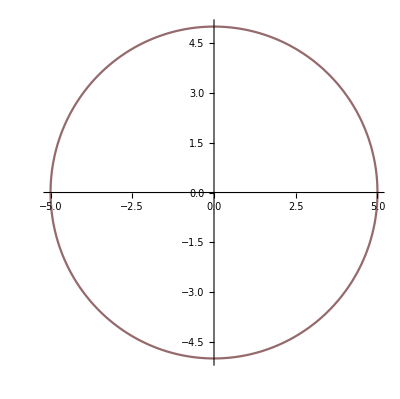

```mathematica
ParametricPlot[{5 cos(t),5 sin(t)},{t,0,2Pi},ColorFunction->"Rainbow"]
```

```mathematica
(a|->a)[1]
```

1

```mathematica
{{{1,2},{2,4}}}/@MatrixForm
```

MatrixForm